```mathematica
toEigenbasis[Uin_, Hin_, tIn_?NumericQ] := (
basis = statesInOrder[Hin /. t->tIn];
basis.Uin /. t->tIn
)
```

0.298002

0.941985

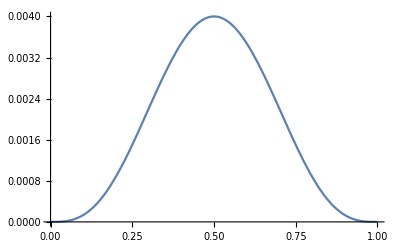

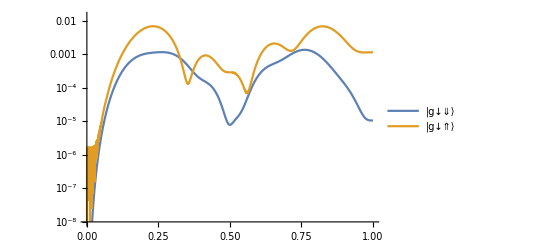

```mathematica
setVariables[]
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,0.004,5.766889065694458*^10,3.51481386083626*^10,1/10000000};

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax/2, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/2, Tmax]^2;

Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];
Uax = (*ConjugateTranspose[Ubase].*)findEvolutionOperator[Hcorrected];
U = Uax/. t->Tmax;

targetGate = {{1, 0}, {0, E^(-ⅈ*angle[U])}};
angle[U]
F = fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]] // Chop

Plot[Bamp[t], {t, 0, Tmax}]
LogPlot[{
1 - Abs[toEigenbasis[Uax, Hcorrected, t][[1, 1]]]^2,
1 - Abs[toEigenbasis[Uax, Hcorrected, t][[2, 2]]]^2
}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotRange->{10^-8, Full}]

clearVariables[]
```